{{x→InterpolatingFunction[{{0., 50.}}, <>]}}

{{x→InterpolatingFunction[{{0., 50.}}, <>]}}

{{x→InterpolatingFunction[{{0., 50.}}, <>]}}

«8 more identical outputs»

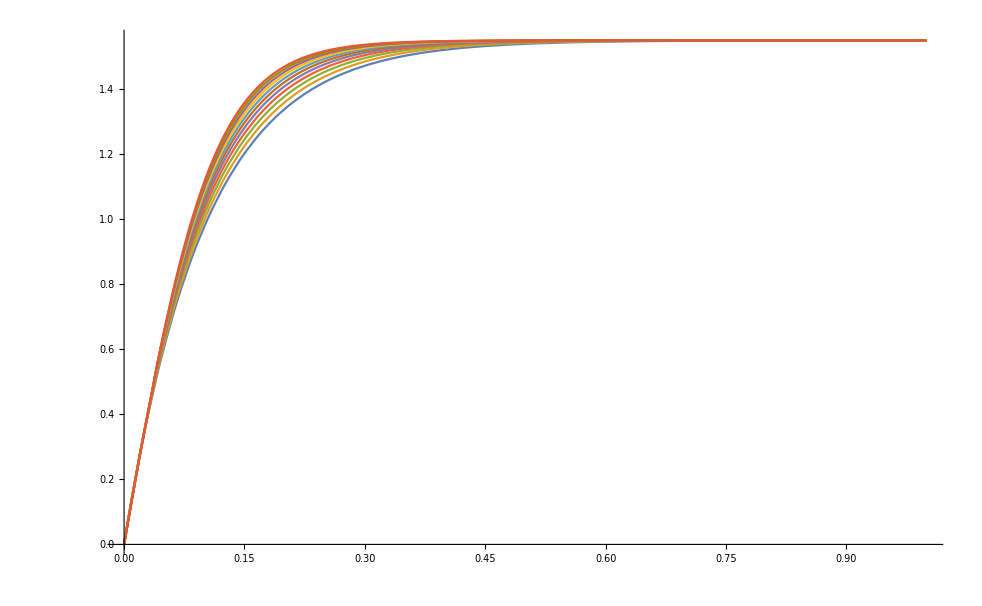

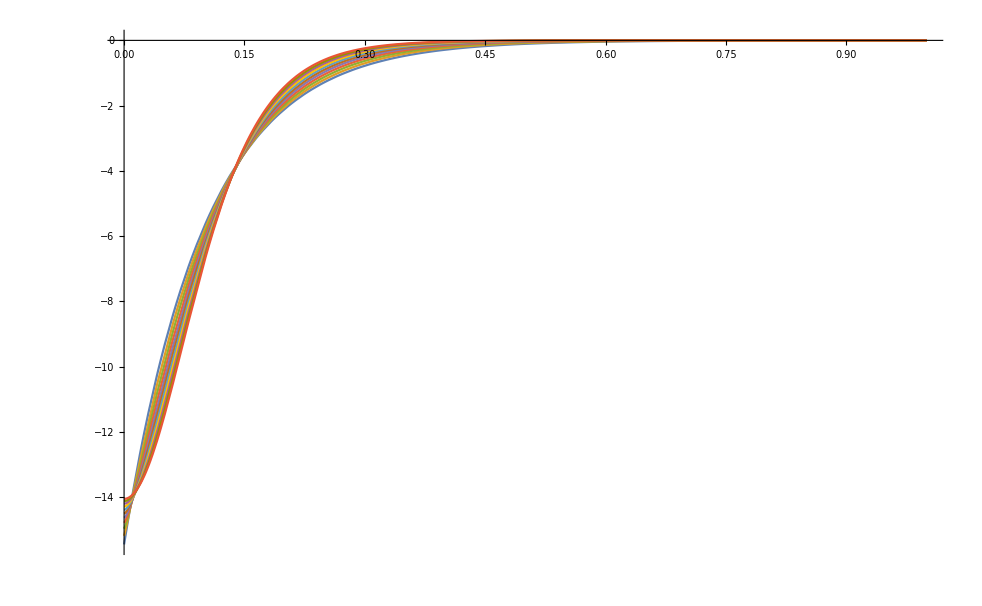

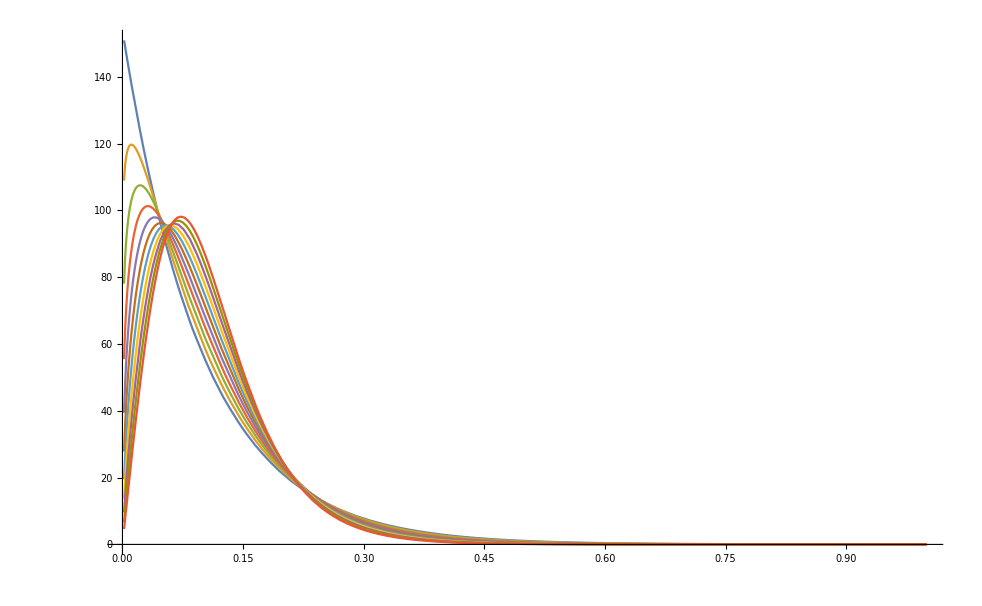

```mathematica
m:=7.11/1000
d:=12/1000
Di:=105/1000
p:=1253
g:=9.81
u:=0.523
cd:=1
solveTime:=50
plotTime:=1
Vt:=1.18*(1-d/Di)^(-2.25)
v[i_]:=cd*x[t]^i
s10=NDSolve[{m*x'[t]==m g -(Pi/6)*p*d^3*g-(Pi/8)*p*d^2*v[1],x[0]==0},x,{t,0,solveTime}]
s11=NDSolve[{m*x'[t]==m g -(Pi/6)*p*d^3*g-(Pi/8)*p*d^2*v[1.1],x[0]==0},x,{t,0,solveTime}]
s12=NDSolve[{m*x'[t]==m g -(Pi/6)*p*d^3*g-(Pi/8)*p*d^2*v[1.2],x[0]==0},x,{t,0,solveTime}]
s13=NDSolve[{m*x'[t]==m g -(Pi/6)*p*d^3*g-(Pi/8)*p*d^2*v[1.3],x[0]==0},x,{t,0,solveTime}]
s14=NDSolve[{m*x'[t]==m g -(Pi/6)*p*d^3*g-(Pi/8)*p*d^2*v[1.4],x[0]==0},x,{t,0,solveTime}]
s15=NDSolve[{m*x'[t]==m g -(Pi/6)*p*d^3*g-(Pi/8)*p*d^2*v[1.5],x[0]==0},x,{t,0,solveTime}]
s16=NDSolve[{m*x'[t]==m g -(Pi/6)*p*d^3*g-(Pi/8)*p*d^2*v[1.6],x[0]==0},x,{t,0,solveTime}]
s17=NDSolve[{m*x'[t]==m g -(Pi/6)*p*d^3*g-(Pi/8)*p*d^2*v[1.7],x[0]==0},x,{t,0,solveTime}]
s18=NDSolve[{m*x'[t]==m g -(Pi/6)*p*d^3*g-(Pi/8)*p*d^2*v[1.8],x[0]==0},x,{t,0,solveTime}]
s19=NDSolve[{m*x'[t]==m g -(Pi/6)*p*d^3*g-(Pi/8)*p*d^2*v[1.9],x[0]==0},x,{t,0,solveTime}]
s20=NDSolve[{m*x'[t]==m g -(Pi/6)*p*d^3*g-(Pi/8)*p*d^2*v[2],x[0]==0},x,{t,0,solveTime}]
s0:=Vt/Evaluate[x[solveTime]/.s10]
s1:=Vt/Evaluate[x[solveTime]/.s11]
s2:=Vt/Evaluate[x[solveTime]/.s12]
s3:=Vt/Evaluate[x[solveTime]/.s13]
s4:=Vt/Evaluate[x[solveTime]/.s14]
s5:=Vt/Evaluate[x[solveTime]/.s15]
s6:=Vt/Evaluate[x[solveTime]/.s16]
s7:=Vt/Evaluate[x[solveTime]/.s17]
s8:=Vt/Evaluate[x[solveTime]/.s18]
s9:=Vt/Evaluate[x[solveTime]/.s19]
s00:=Vt/Evaluate[x[solveTime]/.s20]
Plot[{Evaluate[x[t]*s0/.s10],Evaluate[x[t]*s1/.s11],Evaluate[x[t]*s2/.s12],Evaluate[x[t]*s3/.s13],Evaluate[x[t]*s4/.s14],Evaluate[x[t]*s5/.s15],Evaluate[x[t]*s6/.s16],Evaluate[x[t]*s7/.s17],Evaluate[x[t]*s8/.s18],Evaluate[x[t]*s9/.s19],Evaluate[x[t]*s00/.s20]},{t,0,plotTime},PlotRange->All]

Plot[{Evaluate[-x'[t]*s0/.s10],Evaluate[-x'[t]*s1/.s11],Evaluate[-x'[t]*s2/.s12],Evaluate[-x'[t]*s3/.s13],Evaluate[-x'[t]*s4/.s14],Evaluate[-x'[t]*s5/.s15],Evaluate[-x'[t]*s6/.s16],Evaluate[-x'[t]*s7/.s17],Evaluate[-x'[t]*s8/.s18],Evaluate[-x'[t]*s9/.s19],Evaluate[-x'[t]*s00/.s20]},{t,0,plotTime},PlotRange->All]

Plot[{Evaluate[-x''[t]*s0/.s10],Evaluate[-x''[t]*s1/.s11],Evaluate[-x''[t]*s2/.s12],Evaluate[-x''[t]*s3/.s13],Evaluate[-x''[t]*s4/.s14],Evaluate[-x''[t]*s5/.s15],Evaluate[-x''[t]*s6/.s16],Evaluate[-x''[t]*s7/.s17],Evaluate[-x''[t]*s8/.s18],Evaluate[-x''[t]*s9/.s19],Evaluate[-x''[t]*s00/.s20]},{t,1/500,plotTime},PlotRange->All]
```

```mathematica
√((4 g(6 m-π p d^3))/(3 π p cd d^2))
1.10204*(1-d/Di)^(-2.25)
```

0.909629

1.44806

```mathematica
(1-d/Di)^(-2.25)
```

1.22684

```mathematica
(6 m g-π p d^3 g)/(18 π u d)
(6 m g-π p d^3 g)/(18 π u d)*(1-d/Di)^(-2.25)
```

0.99117

1.30238